```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
filename="10kHz.csv";
data=Import[filename];
```

```mathematica
data[[;;5]]//TableForm
data0=data[[6;;,{1,2}]];
```

#Title | Digilent WaveForms Spectrum Analyzer Data
#Device Name | Analog Discovery
#Serial Number | SN:210244693068
#Software Version | 2.7.5
Frequency (Hz) | Trace 1 (dB)

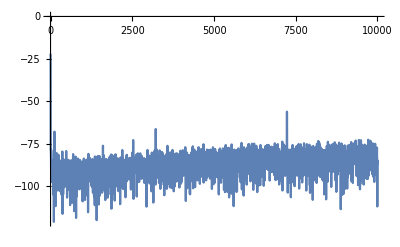

1

```mathematica
ListPlot[data0,Joined->True,PlotRange->All]
cutoff=-30;
posDC=Flatten[Position[Boole[Positive[data0[[;;,2]]-cutoff]],1]][[1]]
```

```mathematica
Clear[att];
att=0;10;(*attenutation in dB *)
W[x_]:=10^((x+att)/10); (*power in W in dB*)
VrefpkpkSA=4 √(Vsq[-11] 1.); (*factor of 4 to get pkpk from fourier amplitude (or factor of 2 if the SA gives 1sided PSD?)*)
VrefpkpkScope=.134; (*-11dB on SA gave .134mVpkpk on scope*)
VtoV=VrefpkpkScope/VrefpkpkSA;

Vsq[x_]:=W[x] 50 ;(*voltage^2 in V^2 *)
us=10^-6;
τ=3.7555us;
FWHM=1/(π τ);
fpkpk=FWHM/√3;
Vpkpk=1.15;
Hzsq[x_]:=(VtoV)^2(fpkpk/Vpkpk)^2 Vsq[x];(*freq^2 in Hz^2*)

f=data0[[;;,1]];
```

fwhm[Hz] | rbw[Hz] | total power up to 10000Hz [Hz^2] | filename
1063.59 | 2.44141 | 204615. | 10kHz.csv

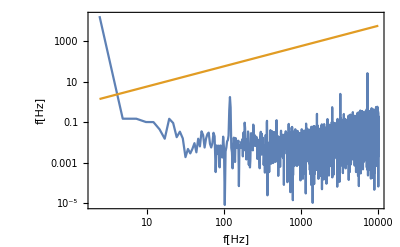

```mathematica
rbw=f[[2]]-f[[1]];

h0=Hzsq[data0[[;;,2]]]/rbw; (*frequency PSD in Hz^2/Hz*)
β[f_]:=8Log[2]f/π^2;
βlist=Table[{ff,β[ff]},{ff,f}];
data1=Thread[{f,h0}]; (*PSD in units of Hz^2/Hz*)

dataDiff=Thread[{f,h0-βlist[[;;,2]]}]; 

A=Total[Boole[Positive[dataDiff[[posDC;;,2]]]]data1[[posDC;;,2]]]rbw; (*area under curve*)
fwhm=√(8 Log[2] A);

HFcut=10^4;
area=Total[Cases[data1,x_/;x[[1]]≤ HFcut][[posDC;;,2]]] rbw;

{{"fwhm[Hz]","rbw[Hz]","total power up to "<>ToString[HFcut]<>"Hz [Hz^2]","filename"},{fwhm,rbw,area,filename}}//TableForm

(*eq 10 from paper,ignoring 0 frequency bin*)

Show[{
ListLogLogPlot[{data1,βlist},Joined->True,Axes->False,Frame->True,FrameLabel->{"f[Hz]","f[Hz]"},FrameStyle->Black,LabelStyle->Medium,PlotRange->{All,{0,10}}]
}]
```

## save

fwhm[Hz] | rbw[Hz] | total power up to 10000Hz [Hz^2] | filename
1063.59 | 2.44141 | 204615. | 10kHz.csv

-Graphics-

## save

fwhm[Hz] | rbw[Hz] | total power up to 10000Hz [Hz^2] | filename
1066.25 | 24.4141 | 205223. | 100kHz.csv

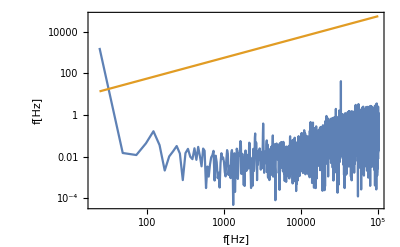

## save

fwhm[Hz] | rbw[Hz] | total power up to 10000Hz [Hz^2] | filename
1091.23 | 244.141 | 214920. | 1MHz.csv

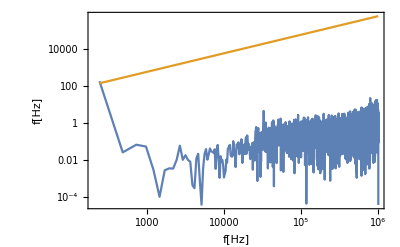

## save

fwhm[Hz] | rbw[Hz] | total power up to 10000Hz [Hz^2] | filename
935.82 | 2441.41 | 198084. | 10MHz.csv